```mathematica
NDSolve[{u'[t]==10*u[t]*(1-u[t]/5)-(u[t]*v[t])/(1+u[t]), v'[t]==(u[t]*v[t])/(1+u[t])-0.1*u[t],u[0]==0.1,v[0]==0.1},{u,v},{t,0,100}]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

NDSolve::nderr: Error test failure at t == 48.4864; unable to continue.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,True,True,True}.

NDSolve[{True,True,True,True},{u,v},{t,0,100}]

{{u→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…]}}

«1 more identical outputs»

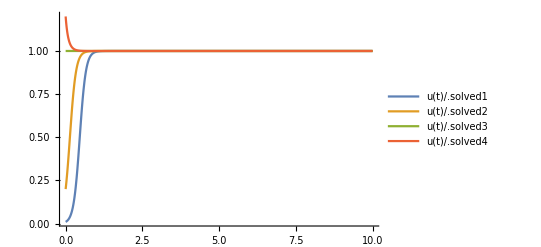

```mathematica
solved1=NDSolve[{u'[t]==10*u[t]*(1-u[t]),u[0]==0.01},u,{t,0,10}]
solved2=NDSolve[{u'[t]==10*u[t]*(1-u[t]),u[0]==0.2},u,{t,0,10}]
solved3=NDSolve[{u'[t]==10*u[t]*(1-u[t]),u[0]==1},u,{t,0,10}]
solved4=NDSolve[{u'[t]==10*u[t]*(1-u[t]),u[0]==1.2},u,{t,0,10}]
Plot[{u[t]/.solved1,u[t]/.solved2,u[t]/.solved3,u[t]/.solved4},{t,0,10},PlotRange->All,PlotLegends->"Expressions"]
```

{{x→InterpolatingFunction[…]}}

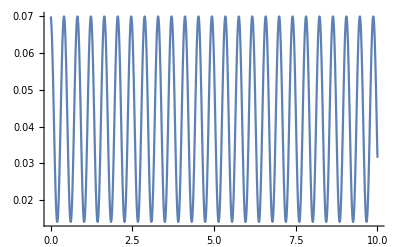

```mathematica
g=9.8;
k=14;
m=0.06;
sol=NDSolve[{x''[t]==g-k*x[t]/m,x[0]==0.07,x'[0]==0},x,{t,0,10}]
tau=0;
While[tau≤10,Plot[x[t]/.sol,{t,0,10}]]
(*Plot[x[t]/.sol,{t,0,10},PlotRange->All,PlotLegends->"Expressions"]*)
```

```mathematica
sol=NDSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[0,t]==1,u[5,t]==0,u[x,0]==If[x≤0.5,1,0]},u,{x,0,5},{t,0,5}]
Plot3D[u[x,t]/.sol,{x,0,5},{t,0,5},AxesLabel->Automatic]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{u→InterpolatingFunction[{{0., 5.}, {0., 5.}}, <>]}}

-Graphics3D-